```mathematica
x[t_] := Cos[t];
y[t_] := Sin[t];
```

```mathematica
NIntegrate[x[t]y'[t]-x'[t]y[t],{t,0, 2Pi}, WorkingPrecision->10]/2
```

3.141592654

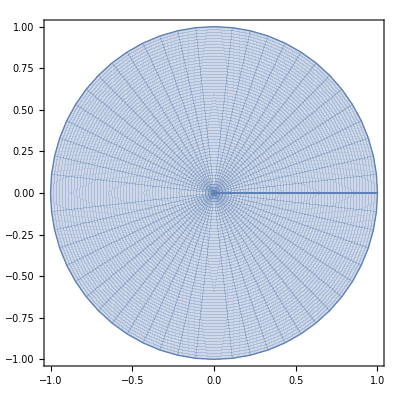

```mathematica
ParametricPlot[{r x[t],r y[t]}, {t, 0, 2Pi}, {r, 0, 1}]
```

```mathematica
`
```